## Reactions

### Exercise 4.C1

The plan here is to abstract the reaction solver, to *hopefully* solve a system of reactions, by invoking equilibrium (assuming statically determinate; though I suppose that statically indeterminate will just return no solution.)

To this we abstract every force to a magnitude, direction, and location.

```mathematica
fArbitrary={"Label", fArbMag, {dx, dy, dz}, {cx,cy,cz}}
```

{Label,fArbMag,{dx,dy,dz},{cx,cy,cz}}

Now the problem:
-Graphics-

We first make a list of all of the forces. We can immediately get the equations for the sum of the forces (in x and y) and the sum of the moments about the origin (point A in this case).

```mathematica
Clear[tMag,aXMag,AYMag,theta]
forceList4C1={
{"PLoad",Quantity[50,"Pounds"],{0,-1,0},Simplify[{27*Sin[theta]+4*Cos[theta],-27*Cos[theta]+4*Sin[theta],0}]},
{"Tension E",tMag,Normalize[{8-12*Sin[theta],16+12*Cos[theta],0}],{12*Sin[theta],-12*Cos[theta],0}},
(*{"Tension E",tMag,{0,1,0},{12*Sin[theta],-12*Cos[theta],0}},*)
{"Ax Reaction",aXMag,{1,0,0},{0,0,0}},
{"Ay Reaction",aYMag,{0,1,0},{0,0,0}} (*,
{"Gravity Bar",gravMag,{dGx,dGy,0},{27*Sin[theta],27*Cos[theta],0}}*)
};

numForces=Length[forceList4C1];
forceNet=Sum[forceList4C1[[i]][[2]]*forceList4C1[[i]][[3]],{i,1,numForces}]
momentNet= Sum[forceList4C1[[i]][[2]]*((forceList4C1[[i]][[4]])×forceList4C1[[i]][[3]]),{i,1,numForces}]
```

{aXMag+0 lb+(tMag (8-12 Sin[theta]))/(√(Abs[16+12 Cos[theta]]^2+Abs[8-12 Sin[theta]]^2)),aYMag+(tMag (16+12 Cos[theta]))/(√(Abs[16+12 Cos[theta]]^2+Abs[8-12 Sin[theta]]^2))+-50 lb,0 lb}

{0 lb,0 lb,(50 lb) (-4 Cos[theta]-27 Sin[theta])+tMag ((96 Cos[theta])/(√(Abs[16+12 Cos[theta]]^2+Abs[8-12 Sin[theta]]^2))+(192 Sin[theta])/(√(Abs[16+12 Cos[theta]]^2+Abs[8-12 Sin[theta]]^2)))}

Invoking Equilibrium, sum of forces and sum of moments equal the zero vectors

```mathematica
StringForm["Invoking Equilibrium, sum of forces and sum of moments"]
Solve[forceNet=={0,0,0},{aXMag,aYMag}]
Solve[momentNet=={0,0,0},{tMag}]

StringForm["Converting to a table"]
sol4C1Flat=Table[
Flatten[
{theta*180/π,{tMag,aXMag,aYMag}/.
Solve[forceNet=={0,0,0}&&momentNet=={0,0,0},{tMag,aXMag,aYMag}]}],{theta,0,120*π/180,10*π/180}];
N[sol4C1Flat]
```

Invoking Equilibrium, sum of forces and sum of moments

{{aXMag→-(8 tMag)/(√(Abs[16+12 Cos[theta]]^2+Abs[8-12 Sin[theta]]^2))+(12 tMag Sin[theta])/(√(Abs[16+12 Cos[theta]]^2+Abs[8-12 Sin[theta]]^2)),aYMag→-(16 tMag)/(√(Abs[16+12 Cos[theta]]^2+Abs[8-12 Sin[theta]]^2))-(12 tMag Cos[theta])/(√(Abs[16+12 Cos[theta]]^2+Abs[8-12 Sin[theta]]^2))+50 lb}}

{{tMag→(√(Abs[16+12 Cos[theta]]^2+Abs[8-12 Sin[theta]]^2) (25/48 lb) (4 Cos[theta]+27 Sin[theta]))/(Cos[theta]+2 Sin[theta])}}

Converting to a table

{{0.,60.6676 lb,-16.6667 lb,-8.33333 lb},{10.,95.9367 lb,-19.9573 lb,-43.8379 lb},{20.,114.835 lb,-16.2366 lb,-63.6815 lb},{30.,125.324 lb,-9.46983 lb,-74.9653 lb},{40.,130.601 lb,-1.4854 lb,-80.5923 lb},{50.,132.224 lb,6.64108 lb,-82.0575 lb},{60.,131.071 lb,14.1693 lb,-80.3032 lb},{70.,127.705 lb,20.5406 lb,-76.0424 lb},{80.,122.545 lb,25.3127 lb,-69.9021 lb},{90.,115.962 lb,28.125 lb,-62.5 lb},{100.,108.367 lb,28.6696 lb,-54.506 lb},{110.,100.338 lb,26.643 lb,-46.7366 lb},{120.,92.9432 lb,21.6246 lb,-40.3925 lb}}

We separate the values into different lists and plot the result

41.8103

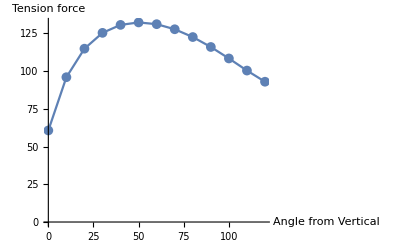

```mathematica
thetaDegVals=sol4C1Flat[[1;;,1]];
tMagVals=sol4C1Flat[[1;;,2]];
aXMagVals=N[sol4C1Flat[[1;;,3]]];
aYMagVals=N[sol4C1Flat[[1;;,4]]];
thetaCrit=ArcSin[8/12]*180/π;
N[thetaCrit]
ListLinePlot[Flatten[{thetaDegVals,tMagVals},{{2},{1}}],AxesLabel->{"Angle from Vertical","Tension force"},PlotRange->All, PlotMarkers->{Automatic, 10}]
```

To check our angles, we can plot the location of the tension force and the load. (It follows the bar movement as a function of theta.

{{0.,4.,-27.},{10.,8.62773,-25.8952},{20.,12.9933,-24.0036},{30.,16.9641,-21.3827},{40.,20.4194,-18.112},{50.,23.2544,-14.2911},{60.,25.3827,-10.0359},{70.,26.7398,-5.47577},{80.,27.2844,-0.74927},{90.,27.,4.},{100.,25.8952,8.62773},{110.,24.0036,12.9933},{120.,21.3827,16.9641}}

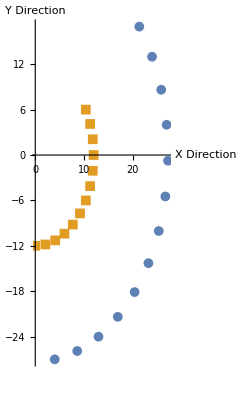

```mathematica
endofLrod=N[Table[{theta*180/π,27*Sin[theta]+4*Cos[theta],-27*Cos[theta]+4*Sin[theta]},{theta,0,120*π/180,10*π/180}]]
endofLrod[[1;;,2;;3]];
midofRod=N[Table[{theta*180/π,12*Sin[theta], -12*Cos[theta]},{theta,0,120*π/180,10*π/180}]];
ListPlot[{endofLrod[[1;;,2;;3]],midofRod[[1;;,2;;3]]},AspectRatio->Automatic,AxesLabel->{"X Direction","Y Direction"}, PlotMarkers->{Automatic, 10}]
```